```mathematica
(* examine the asymptotic series of the Fisher information after the quadratic stage *)
```

```mathematica
(* useful quantities for the sums in the Fisher information *)
f$rules = {
f1->I(PolyGamma[0,1 + k + I Sqrt[c0]]-PolyGamma[0, 1+k - I Sqrt[c0]]),
f2->PolyGamma[0,1 + k + I Sqrt[c0]]+PolyGamma[0, 1+k - I Sqrt[c0]]
}
c0$rule = {
c0->(sigmaM^2 + 2s^2)/(2 sigmaC^2)
}
c$rules = {
c1->I(PolyGamma[0,1+I Sqrt[c0]]-PolyGamma[0, 1-I Sqrt[c0]]),
c2->PolyGamma[0,1+I Sqrt[c0]]+PolyGamma[0, 1-I Sqrt[c0]]
}
```

{f1→ⅈ (-PolyGamma[0,1-ⅈ √c0+k]+PolyGamma[0,1+ⅈ √c0+k]),f2→PolyGamma[0,1-ⅈ √c0+k]+PolyGamma[0,1+ⅈ √c0+k]}

{c0→(2 s^2+sigmaM^2)/(2 sigmaC^2)}

{c1→ⅈ (-PolyGamma[0,1-ⅈ √c0]+PolyGamma[0,1+ⅈ √c0]),c2→PolyGamma[0,1-ⅈ √c0]+PolyGamma[0,1+ⅈ √c0]}

```mathematica
prefactor = n/(2sigmaC^2 k)
```

n/(2 k sigmaC^2)

```mathematica
(* Fisher information quantities *)
vw0=prefactor * (-1/(2 Sqrt[c0]) * c1+ 1/(2 Sqrt[c0])* f1) ;
vw1= prefactor*(-c2/2 + f2/2) ;
vw2=n/(2 sigmaC^2) + prefactor * (Sqrt[c0]/2  * c1 - Sqrt[c0]/2  * f1);
vw3= n/(4 sigmaC^2)(1 + k) + prefactor*c0*(c2/2- f2/2);
vw4 = n/(12 sigmaC^2)(1 - 6c0 + 3k + 2k^2)+(n c0^(3/2))/(4 sigmaC^2 k)(f1 -c1);
```

```mathematica
(* calculate sums *)
vw0$sum =n/(2 sigmaC^2 k)Sum[1/(c0+i^2),{i,1,k}];
vw1$sum=n/(2 sigmaC^2 k)Sum[i/(c0+i^2),{i,1,k}];
vw2$sum=n/(2 sigmaC^2 k)Sum[i^2/(c0+i^2),{i,1,k}];
vw3$sum =n/(2 sigmaC^2 k)Sum[i^3/(c0+i^2),{i,1,k}];
vw4$sum =n/(2 sigmaC^2 k) Sum[i^4/(c0+i^2),{i,1,k}];
```

```mathematica
(* check calculations *)
vw0/.f$rules/.c$rules/.c0$rule/.s->1.3/.sigmaM->2/.sigmaC->5/.k->2/.n->13//N//Chop
vw0$sum/.c0$rule/.s->1.3/.sigmaM->2/.sigmaC->5/.k->2/.n->13//N//Chop
vw1/.f$rules/.c$rules/.c0$rule/.s->1.3/.sigmaM->2/.sigmaC->5/.k->2/.n->13//N//Chop
vw1$sum/.c0$rule/.s->1.3/.sigmaM->2/.sigmaC->5/.k->2/.n->13//N//Chop
vw2/.f$rules/.c$rules/.c0$rule/.s->1.3/.sigmaM->2/.sigmaC->5/.k->2/.n->13//N//Chop
vw2$sum/.c0$rule/.s->1.3/.sigmaM->2/.sigmaC->5/.k->2/.n->13//N//Chop
vw3/.f$rules/.c$rules/.c0$rule/.s->1.3/.sigmaM->2/.sigmaC->5/.k->2/.n->13//N//Chop
vw3$sum/.c0$rule/.s->1.3/.sigmaM->2/.sigmaC->5/.k->2/.n->13//N//Chop
vw4/.f$rules/.c$rules/.c0$rule/.s->1.3/.sigmaM->2/.sigmaC->5/.k->2/.n->13//N//Chop
vw4$sum/.c0$rule/.s->1.3/.sigmaM->2/.sigmaC->5/.k->2/.n->13//N//Chop
```

0.144623

0.144623

0.175967

0.175967

0.238654

0.238654

0.364027

0.364027

0.614775

0.614775

```mathematica
(* calculate total Fisher information *)
alpha$rule = {alpha->(s^2 sigmaC^2/(sigmaM^4 + 2s^2 sigmaC^2 sigmaM^2 vw2))};
VMV = vw0/(2 sigmaM^2) - alpha vw1^2;
WMW = vw4/(2 sigmaM^2) - alpha vw3^2;
VMW = vw2/(2 sigmaM^2) - alpha vw3 vw1;
```

```mathematica
fisher$info = Simplify[4s^2(VMV - 2sigmaC^4/(1+ 2sigmaC^4 WMW) * VMW^2)]
```

1/(4 k^2 sigmaC^4)n s^2 (-alpha (c2-f2)^2 n-(2 (c1-f1) k sigmaC^2)/(√c0 sigmaM^2)+(3 n (2 √c0 (c1-f1) k sigmaC^2+alpha c0 (c2-f2)^2 n sigmaM^2+k (4 k sigmaC^2+alpha (c2-f2) n sigmaM^2+alpha (c2-f2) k n sigmaM^2))^2)/(sigmaM^2 (6 c0^(3/2) (c1-f1) k n sigmaC^2+3 alpha c0^2 (c2-f2)^2 n^2 sigmaM^2+6 c0 k n (2 k sigmaC^2+alpha (c2-f2) n sigmaM^2+alpha (c2-f2) k n sigmaM^2)+k^2 (-2 (1+3 k+2 k^2) n sigmaC^2-24 sigmaM^2+3 alpha (1+k)^2 n^2 sigmaM^2))))

```mathematica
(* apply simplification rules; alt corresponds to when k scales as N *)
fisher$simplified=Simplify[fisher$info/.alpha$rule/.f$rules];
fisher$simplified$alt = Simplify[fisher$info/.alpha$rule/.f$rules/.k->(n/k)];
```

```mathematica
(* expand series around infinity *)
fisher$series = Series[fisher$simplified,{n,Infinity,3}]
```

(s^2 (-(c1+ⅈ PolyGamma[0,1-ⅈ √c0+k]-ⅈ PolyGamma[0,1+ⅈ √c0+k])/(√c0)+(ⅈ 1^2)/1-(3 sigmaC^2 (c0 c1^2 s^2+6+1)^2)/((√c0 c1 s^2+2 k s^2+ⅈ √c0 1 1-ⅈ √c0 s^2 PolyGamma[0,1+ⅈ √c0+k]) (1))) n)/(2 k sigmaC^2 sigmaM^2)+(s^2 ((2 k sigmaM^2 (1)^2)/(s^2 (1)^2)-3 6^2 (-((1) 1)/((1) 1)+1)))/(2 k sigmaC^2 sigmaM^2)+(s^2 (-1/1-1))/(2 k sigmaC^2 sigmaM^2 n)+(s^2 (1))/(2 3 n^2)+(s^2 (1))/(2 k sigmaC^2 sigmaM^2 n^3)+O[1/n]^4
 |  |  |  |

```mathematica
n$coefficient = Coefficient[fisher$series, n]/.c$rules/.c0$rule//Simplify;
n$coefficient$simplified = n$coefficient/.sigmaC->1/.s->1;
```

```mathematica
sigmaM$1 = Table[Chop[n$coefficient$simplified/.sigmaM->1//N], {k,1,25}];
sigmaM$2= Table[Chop[n$coefficient$simplified/.sigmaM->2//N], {k,1,25}];
sigmaM$3 = Table[Chop[n$coefficient$simplified/.sigmaM->3//N], {k,1,25}];
```

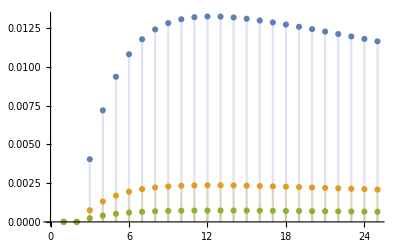

```mathematica
(* Plot linear coefficients for various noise terms *)
DiscretePlot[{Re[n$coefficient$simplified/.sigmaM->1],Re[n$coefficient$simplified/.sigmaM->2], Re[n$coefficient$simplified/.sigmaM->3]}, {k, 1, 25}, PlotRange->All]
```

```mathematica
(* expand series around infinity for k scaling as N *)
fisher$series$alt = Series[fisher$simplified/.k->n,{n,Infinity,3}]
```

-(c1 s^2)/(2 (√c0 sigmaC^2 sigmaM^2))-(s^2 (13+6 c2+c2^2-12 Log[n]-4 c2 Log[n]+4 Log[n]^2))/(sigmaC^2 sigmaM^2 n)+1/(2 sigmaC^2 sigmaM^2 n^2)(13 s^2+12 √c0 c1 s^2-8 c2 s^2+18 √c0 c1 c2 s^2-3 c2^2 s^2+4 √c0 c1 c2^2 s^2+72 sigmaM^2+48 c2 sigmaM^2+8 c2^2 sigmaM^2+16 s^2 Log[n]-36 √c0 c1 s^2 Log[n]+12 c2 s^2 Log[n]-16 √c0 c1 c2 s^2 Log[n]-96 sigmaM^2 Log[n]-32 c2 sigmaM^2 Log[n]-12 s^2 Log[n]^2+16 √c0 c1 s^2 Log[n]^2+32 sigmaM^2 Log[n]^2)+1/(6 s^2 sigmaC^2 sigmaM^2 n^3)(-49 s^4-754 c0 s^4+162 √c0 c1 s^4-126 c0 c1^2 s^4-20 c2 s^4-744 c0 c2 s^4+138 √c0 c1 c2 s^4-108 c0 c1^2 c2 s^4-9 c2^2 s^4-282 c0 c2^2 s^4+36 √c0 c1 c2^2 s^4-24 c0 c1^2 c2^2 s^4-36 c0 c2^3 s^4+288 s^2 sigmaM^2-648 √c0 c1 s^2 sigmaM^2+312 c2 s^2 sigmaM^2-504 √c0 c1 c2 s^2 sigmaM^2+72 c2^2 s^2 sigmaM^2-96 √c0 c1 c2^2 s^2 sigmaM^2-864 sigmaM^4-576 c2 sigmaM^4-96 c2^2 sigmaM^4+40 s^4 Log[n]+1488 c0 s^4 Log[n]-276 √c0 c1 s^4 Log[n]+216 c0 c1^2 s^4 Log[n]+36 c2 s^4 Log[n]+1128 c0 c2 s^4 Log[n]-144 √c0 c1 c2 s^4 Log[n]+96 c0 c1^2 c2 s^4 Log[n]+216 c0 c2^2 s^4 Log[n]-624 s^2 sigmaM^2 Log[n]+1008 √c0 c1 s^2 sigmaM^2 Log[n]-288 c2 s^2 sigmaM^2 Log[n]+384 √c0 c1 c2 s^2 sigmaM^2 Log[n]+1152 sigmaM^4 Log[n]+384 c2 sigmaM^4 Log[n]-36 s^4 Log[n]^2-1128 c0 s^4 Log[n]^2+144 √c0 c1 s^4 Log[n]^2-96 c0 c1^2 s^4 Log[n]^2-432 c0 c2 s^4 Log[n]^2+288 s^2 sigmaM^2 Log[n]^2-384 √c0 c1 s^2 sigmaM^2 Log[n]^2-384 sigmaM^4 Log[n]^2+288 c0 s^4 Log[n]^3)+O[1/n]^4

```mathematica
(* validate that the Fisher information saturates *)
Coefficient[fisher$series$alt, n, 1]
Coefficient[fisher$series$alt, n, 0]
```

0

-(c1 s^2)/(2 √c0 sigmaC^2 sigmaM^2)

```mathematica
Export["coefficients.h5", {sigmaM$1, sigmaM$2, sigmaM$3}, {"Datasets", {"sigmaM1", "sigmaM2", "sigmaM3"}}]
```

coefficients.h5